```mathematica
(*Van Gogh style*)
img=Import["http://i.stack.imgur.com/XwYg7.jpg"];

im=img~ImageResize~200~ColorConvert~"Grayscale";

gof=im~GradientOrientationFilter~5;

lines=MapIndexed[{GrayLevel@RandomReal[],Line[{#2-2 {Cos[#1],Sin[#1]},#2+2 {Cos[#1],Sin[#1]}}]}&,Reverse/@Transpose@ImageData@gof,{2}];

brush=Image[Graphics[lines,PlotRange->{{1,#1},{1,#2}}&@@ImageDimensions[im],Background->GrayLevel[0.5],ImageSize->ImageDimensions[img]],ColorSpace->"Grayscale"];
```

```mathematica
brush
```

-Graphics-

```mathematica
img
```

-Graphics-

```mathematica
tm=Image`ToneMapHDRI[img,Method->{"AdaptiveLog","Bias"->1.0}];
```

```mathematica
tm
```

Image`ToneMapHDRI[-Graphics-,Method→{AdaptiveLog,Bias→1.}]

```mathematica
Image[0.7 (ImageData@Blur[brush,2]-0.6)+ImageData@tm]
```

ImageData::imginv: Expecting an image or graphics instead of ….

$Aborted

```mathematica
(*Vectorization in fun ways, with animation*)
```

```mathematica
gimg=ColorConvert[ImageResize[Import["http://i.stack.imgur.com/wtgxH.jpg"],300],"Grayscale"];
```

```mathematica
data=MapIndexed[Append[#2,#1]&,ImageData[gimg],{2}];
```

```mathematica
Table[Rotate[ListDensityPlot[(MapThread[Append,{3 RandomReal[{-1,1},{Length[#],2}],ConstantArray[0,Length[#]]}]+#)&@Flatten[Transpose@data,1][[1;;-1;;15]],InterpolationOrder->0,ColorFunction->"GrayTones",BoundaryStyle->Directive[Black,Opacity[.2]],Frame->False,PlotRangePadding->0,AspectRatio->Automatic,ImageSize->600],-Pi/2],{10}];

Export["test.gif",%]
```

```mathematica
(*colorization*)
```

```mathematica
Grid[Partition[Rotate[ListDensityPlot[(MapThread[Append,{3 RandomReal[{-1,1},{Length[#],2}],ConstantArray[0,Length[#]]}]+#)&@Flatten[Transpose@data,1][[1;;-1;;45]],InterpolationOrder->0,ColorFunction->#,BoundaryStyle->Directive[Black,Opacity[.2]],Frame->False,PlotRangePadding->0,AspectRatio->Automatic,ImageSize->300],-Pi/2]&/@{"CherryTones","CoffeeTones","DarkRainbow","DeepSeaColors","PlumColors","Rainbow","StarryNightColors","SunsetColors","ValentineTones"},3],Spacings->0]
```

```mathematica
(*animation*)
id=ParallelTable[Rotate[ListDensityPlot[(MapThread[Append,{SeedRandom[1];
200 (1-st^(1/8)) RandomReal[{-1,1},{Length[#],2}],ConstantArray[0,Length[#]]}]+#)&@Flatten[Transpose@data,1][[1;;-1;;15]],InterpolationOrder->0,ColorFunction->GrayLevel,BoundaryStyle->Opacity[.1],Frame->False,PlotRangePadding->0,AspectRatio->Automatic,ImageSize->350],-Pi/2],{st,0.2,1,.05}];

idd=id~Join~Table[id[[-1]],{7}];

Export["appear.gif",idd,ImageSize->350]
```

```mathematica
(*Periodic Tiling*)
```

```mathematica
TranslateObject[p_,{x_,y_}]:=Map[{x,y}+#&,p,{2}]

HouseHexPolygon[s_,0]:=Polygon[s*{{1/2,-1},{3/2,0},{3/2,1},{-1/2,1},{-3/2,0},{-3/2,-1}}]
HouseHexPolygon[s_,1]:=Polygon[s*{{1,1/2},{0,3/2},{-1,3/2},{-1,-1/2},{0,-3/2},{1,-3/2}}]

HouseHexGrid[s_,imax_,jmax_]:=Block[{imod,jmod,k,m},Flatten[Table[imod=Mod[2 i,5];
jmod=Mod[2 i+3,5];
k=Range[0,Floor[(jmax-imod)/5]];
m=Range[0,Floor[(jmax-jmod)/5]];
{Table[TranslateObject[HouseHexPolygon[s,0],s*{i+1/2,j}],{j,jmod+1/2+5*m}],Table[TranslateObject[HouseHexPolygon[s,1],s*{i,j}],{j,imod+5*k}]},{i,0,imax}],2]]

HouseHexGridPerturbed[s_,h_,v_,r_]:=Block[{poly=Map[Round[#,10.^-10]&,HouseHexGrid[N[s],h,v],{2}],pts,len,rules},pts=DeleteDuplicates[Flatten[poly[[All,1]],1]];
len=Length[pts];
rules=Dispatch[Thread[pts->Range[len]]];
GraphicsComplex[pts+RandomReal[{-r,r},{len,2}],RandomSample[poly]/.rules]]

HouseHexColourCentroid[image_Image,s_,t_,opts___]:=Block[{d,dim,g,centroids,colours,rr,gg,bb,greys},d=Reverse[ImageData[image]];(*Reverse to get bottom of image on bottom*)dim=Dimensions[d];(*dim[[1]] is number of rows,dim[[2]] is number of cols*)g=HouseHexGridPerturbed[s,Floor[dim[[2]]/s-3],Floor[dim[[1]]/s-3],0];
centroids=Apply[Mean[g[[1,#]]]&,g[[2]],1];
colours=Apply[RGBColor,Extract[d,Map[Reverse,Round[centroids+s/2]]],1];
greys=colours/.RGBColor[rr_,gg_,bb_]->0.299 rr+0.587 gg+0.114 bb;
g[[2]]=Transpose[{colours,g[[2]]}][[Ordering[t*greys]]];
Graphics[{EdgeForm[{Thickness[0.0003],Black}],GraphicsComplex[g[[1]],g[[2]]]},{opts}]]
```

```mathematica
HouseHexColourCentroid[Import["http://www.eso.org/public/archives/images/screen/eso1205a.jpg"],3,1]
```

```mathematica
(*broken vectorization*)
```

```mathematica
findBestCandidate[samplePoints_,nrOfCandidates_,{w_,h_}]:=Module[{nearestFunction,candidates},nearestFunction=Nearest[samplePoints];
candidates=Transpose[{RandomInteger[{1,w},nrOfCandidates],RandomInteger[{1,h},nrOfCandidates]}];
Last@SortBy[candidates,Norm[#-First@nearestFunction@#]&]]

sample[nrOfSamplePoints_,nrOfCandidates_,{w_,h_}]:=Nest[#~Append~findBestCandidate[#,nrOfCandidates,{w,h}]&,{{RandomInteger[w],RandomInteger[h]}},nrOfSamplePoints]
```

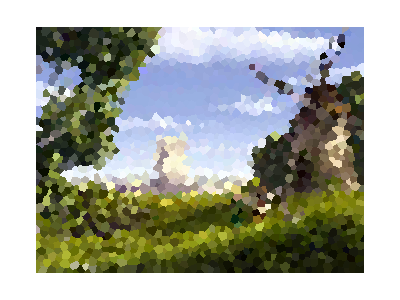

```mathematica
{w,h}=ImageDimensions[img];
pts=sample[2000,20,{w,h}];
mesh=VoronoiMesh[pts,{{0,w},{0,h}}];
coords=MeshPrimitives[mesh,0];
polys=MeshPrimitives[mesh,2];
colorList=RGBColor@@Extract[ImageData[img,DataReversed->True],Reverse@#]&/@(Mean@@@List@@@polys/.x_?NumericQ:>Round[x]);
Graphics[Transpose@{colorList,polys}]
```

```mathematica
Needs["ComputationalGeometry`"]
{w,h}=ImageDimensions[img];
{coords,polys}=BoundedDiagram[{{0,0},{0,h},{w,0},{w,h}},pts];
colorList=MapIndexed[First@#2->RGBColor@@Extract[ImageData[img,DataReversed->True],Reverse@#]&,pts];
Graphics[{First@#/.colorList,GraphicsComplex[coords,Polygon@Last@#]}&/@polys]
```

Set::shape: Lists {coords,polys} and BoundedDiagram[{{0,0},{0,768},{1024,0},{1024,768}},sample[2000,20,{1024,768}]] are not the same shape.

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[2000].

Extract::psl1: Position specification Reverse[2000] in Extract[{{{0.458824,0.443137,0.054902},«49»,«974»},{«1»},«47»,{«1»},«718»},«1»] is not applicable.

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[20].

Extract::psl1: Position specification Reverse[20] in Extract[{{{0.458824,0.443137,0.054902},«49»,«974»},{«1»},«47»,{«1»},«718»},«1»] is not applicable.

ReplaceAll::reps: {sample[1→RGBColor[{{{0.458824,0.443137,0.054902},«49»,«974»},«50»},«1»],«1»,3→«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

First::normal: Nonatomic expression expected at position 1 in First[2].

ReplaceAll::reps: {sample[1→RGBColor[{{{0.458824,0.443137,0.054902},«49»,«974»},«50»},«1»],«1»,3→«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Last::normal: Nonatomic expression expected at position 1 in Last[2].

-Graphics-